```mathematica
Clear[a,b,θ];

(*Logarithmic spiral*)
r[θ_]:={a Exp[b θ] Cos[θ],a Exp[b θ] Sin[θ]};

(*First derivative*)
rp[θ_]:=D[r[ϕ],ϕ]/.ϕ->θ;

(*Speed*)
speed[θ_]:=Sqrt[rp[θ].rp[θ]];

(*Unit tangent*)
T[θ_]:=Simplify[rp[θ]/speed[θ]];

(*Derivative of the tangent*)
Tp[θ_]:=D[T[ϕ],ϕ]/.ϕ->θ;

(*Unit normal (renamed from N!)*)
NormalVec[θ_]:=Simplify[Tp[θ]/Sqrt[Tp[θ].Tp[θ]]];

(*Verify orthogonality T·N=0*)
CheckOrthogonality=Simplify[T[θ].NormalVec[θ]];
```

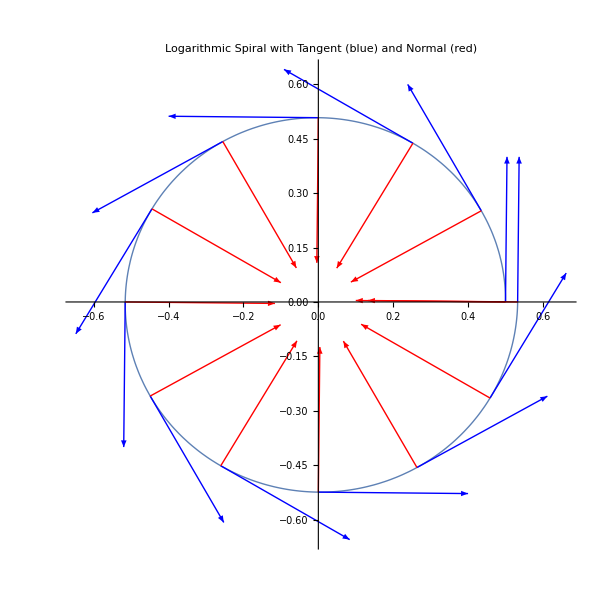

```mathematica
aval=0.5;
bval=0.01;

θmin=0;
θmax=2 Pi;

(*Scaling factor for vectors (for visibility)*)
vecScale=0.4;

(*Numerical versions for plotting*)
rNum[θ_]:=r[θ]/.{a->aval,b->bval};
TNum[θ_]:=T[θ]/.{a->aval,b->bval};
NNum[θ_]:=NormalVec[θ]/.{a->aval,b->bval};

(*Create tangent and normal arrows*)
tangentArrows=Table[Arrow[{rNum[θ],rNum[θ]+vecScale TNum[θ]}],{θ,θmin,θmax,Pi/6}];

normalArrows=Table[Arrow[{rNum[θ],rNum[θ]+vecScale NNum[θ]}],{θ,θmin,θmax,Pi/6}];

(*FINAL PLOT*)
Show[{ParametricPlot[rNum[θ],{θ,θmin,θmax},PlotStyle->Thick,PlotRange->All],Graphics[{Blue,Thick,tangentArrows,Red,Thick,normalArrows}]},Axes->True,AspectRatio->1,ImageSize->600,PlotLabel->"Logarithmic Spiral with Tangent (blue) and Normal (red)"]
```

```mathematica
NormalVec[0]/.{a->aval,b->bval}
```

{-0.980581,0.196116}

```mathematica
Z={0,0,1};
Rot[φ_]:={{Cos[φ],-Sin[φ],0},{Sin[φ],Cos[φ],0},{0,0,1}};
F[θ_]:=Rot[θ/2].(Append[NormalVec[θ],0]+Z)
X[θ_,w_]:=Append[r[θ],0]+w F[θ];
```

{ⅇ^(0.2 θ) Cos[θ]+w (-(0.980581 ⅇ^(0.2 θ) Sin[θ/2] (0.2 Cos[θ]-Sin[θ]))/(√(ⅇ^(0.4 θ)))-(0.980581 ⅇ^(0.2 θ) Cos[θ/2] (Cos[θ]+0.2 Sin[θ]))/(√(ⅇ^(0.4 θ)))),w ((0.980581 ⅇ^(0.2 θ) Cos[θ/2] (0.2 Cos[θ]-Sin[θ]))/(√(ⅇ^(0.4 θ)))-(0.980581 ⅇ^(0.2 θ) Sin[θ/2] (Cos[θ]+0.2 Sin[θ]))/(√(ⅇ^(0.4 θ))))+ⅇ^(0.2 θ) Sin[θ],w}

```mathematica
ParametricPlot3D[X[θ,w],{θ,0,2Pi},{w,0,1},PlotPoints->{200,15},Mesh->None,PlotRange->All,Lighting->"Neutral",ColorFunction->Function[{θ,w,x,y,z},ColorData["Rainbow"][w/W]],Axes->True,Boxed->False,ImageSize->Large]
```

```mathematica
Clear[a,b,θ,w,Nv]

(*PARAMETERS*)
a=1;
b=0.5;
W=1;(*half-width of fibers*)θmin=0;
θmax=1.25Pi;(*3 turns of the spiral*)(*---SPIRAL---*)r[θ_]:=a Exp[b θ] {Cos[θ],Sin[θ],0};

(*---TANGENT AND NORMAL (Frenet-style)---*)
rp[θ_]:=D[r[θ],θ];
T[θ_]:=Normalize[rp[θ]];
Tp[θ_]:=D[T[θ],θ];
N[θ_]:=Normalize[Tp[θ]];
Nv[θ_]:=Tp[θ]/(Norm[Tp[θ]]+10^-8)


(*---VERTICAL DIRECTION---*)
Z={0,0,1};

(*---ROTATION ABOUT Z AXIS---*)
Rot[φ_]:={{Cos[φ],-Sin[φ],0},{Sin[φ],Cos[φ],0},{0,0,1}};

(*---ROTATING FRAME VECTOR---*)
F[θ_]:=Rot[θ].(N[θ]+Z);

(*---POINT ON THE BUNDLE---*)
X[θ_,w_]:=r[θ]+w F[θ];

(*---3D SURFACE PLOT---*)
ParametricPlot3D[X[θ,w],{θ,θmin,θmax},{w,0,W},PlotPoints->{200,15},Mesh->None,PlotRange->All,Lighting->"Neutral",ColorFunction->Function[{θ,w,x,y,z},ColorData["Avocado"][w/W]],Axes->True,Boxed->False,ImageSize->Large]
```

N::nosym: N[θ_] does not contain a symbol to attach a rule to.

ColorData::notent: Avocado is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

-Graphics3D-